# Figure 2

Data are imported from julia code https://github.com/djuliannader/RabiModel

#### Data

```mathematica
(*R=50*)
DatNegR50={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,1*10^(-6)},{0.95,9.6*10^(-5)},{1,0.0028721938315612316},{1.025,0.012356555259824376},{1.05,0.045046985365931436},{1.075,0.1307916991903315},{1.1,0.2733874102764575},{1.125,0.38936523329485073},{1.15,0.4362242778645884},{1.175,0.4460885111407016},{1.2,0.44040837488184037},{1.25,0.41433117514498274},{1.3,0.38455247706474105},{1.35,0.35639368013159256},{1.4,0.33087341966824346},{1.45,0.30794844862649895},{1.5,0.28734309709107686},{1.55,0.2687654993931692},{1.6,0.25195532747756655},{1.65,0.23669221450165723},{1.7,0.22278777508091752},{1.75,0.21007710233871846},{1.8,0.19843810833889042},{1.85,0.1869269263497304},{1.9,0.17789491169926075},{1.95,0.16879059428329657},{2,0.1603653371543292}};
DatPurR50={{0,1},{0.05,0.9999759424382747},{0.1,0.9999034272558528},{0.15,0.9997814087135403},{0.2,0.9996080810591991},{0.25,0.999380776762398},{0.3,0.9990958075749397},{0.35,0.9987482279968808},{0.4,0.9983314878694249},{0.45,0.9978369196052229},{0.5,0.9972529689231903},{0.55,0.996564011762457},{0.6,0.9957484746508471},{0.65,0.994775725143428},{0.7,0.9936006656401877},{0.75,0.9921537418880904},{0.8,0.9903210142961318},{0.85,0.9879003610322292},{0.9,0.9844922503337201},{0.95,0.9791771590785479},{1,0.9693224813794615},{1.025,0.9603014280895678},{1.05,0.9450674965437998},{1.075,0.9184515579592468},{1.1,0.8785402990262056},{1.125,0.8367710422842245},{1.15,0.8026871790347999},{1.175,0.7750621854308072},{1.2,0.7514555074649951},{1.25,0.7121302675708026},{1.3,0.6805020299580149},{1.35,0.6546746928544679},{1.4,0.6333677520262117},{1.45,0.6156417139444618},{1.5,0.600786672980406},{1.55,0.5882553764843841},{1.6,0.5776228874870241},{1.65,0.5685489740866942},{1.7,0.5607683254538206},{1.75,0.5540913609047422},{1.8,0.5482842532028399},{1.85,0.547209527765898},{1.9,0.538855080298695},{1.95,0.5350590376220995},{2,0.5316210729540178}};
DatCocR50={{0,0.7499999999999998/(3*(0.4999999999999999)^2)},{0.05,0.75187881532106897/(3*0.5006258878683949^2)},{0.1,0.7575702173461962/(3*0.5025171970312261^2)},{0.15,0.7672430711295672/(3*0.5057156865326069^2)},{0.2,0.7811926858842599/(3*0.5102937934627627^2)},{0.25,0.7998636425150817/(3*0.5163592513308773^2)},{0.3,0.8238862783538767/(3*0.5240623516549455^2)},{0.35,0.8541326243608005/(3*0.5336068437488745^2)},{0.4,0.8918015616587754/(3*0.5452661080007922^2)},{0.45,0.9385498275352047/(3*0.5594073064848732^2)},{0.5,0.996697933655965/(3*0.5765280821003401^2)},{0.55,1.0695636551744288/(3*0.5973137902315173^2)},{0.6,1.1620228587208135/(3*0.6227297910696789^2)},{0.65,1.2814970798851983/(3*0.6541765798996451^2)},{0.7,1.4397927565972026/(3*0.693764110355717^2)},{0.75,1.6567702540922875/(3*0.744828134343037^2)},{0.8,1.9683184699322553/(3*0.8129808049796601^2)},{0.85,2.445693875973183/(3*0.9084715246222741^2)},{0.9,3.2496856720845577/(3*1.0522287176106724^2)},{0.95,4.8151561325445025/(3*1.2942812620568696^2)},{1,8.676709177081129/(3*1.7849882071835745^2)},{1.025,13.191130472442584/(3*2.2674391149095015^2)},{1.05,22.631175113336358/(3*3.1320410019378047^2)},{1.075,43.84346854342823/(3*4.753957890115041^2)},{1.1,86.54058048100657/(3*7.410067949519209^2)},{1.125,148.84634210202725/(3*10.493667021321095^2)},{1.15,220.15169859326082/(3*13.300979254959833^2)},{1.175,298.0586531970737/(3*15.832025942614708^2)},{1.2,383.911126000021/(3*18.228560986896323^2)},{1.25,582.5198428458652/(3*22.858291957216757^2)},{1.3,818.4428985824297/(3*27.38980353593512^2)},{1.35,1092.5948047408485/(3*31.877910055932638^2)},{1.4,1406.17855195663/(3*36.35409907025217^2)},{1.45,1760.7759077694393/(3*40.84098049841334^2)},{1.5,2158.2884623808554/(3*45.35588629225168^2)},{1.55,2600.874994032024/(3*49.912668152907095^2)},{1.6,3090.9451497954847/(3*54.522313513662965^2)},{1.65,3631.0354456672376/(3*59.19451141631789^2)},{1.7,4223.937966769323/(3*63.936610365068354^2)},{1.75,4964.608564499193/(3*69.40134670548123^2)},{1.8,5580.401624562337/(3*73.65252497015442^2)},{1.85,6452.280035530374/(3*78.98110097928066^2)},{1.9,7184.645185183218/(3*83.71637627393808^2)},{1.95,8089.722951897358/(3*88.8786945024876^2)},{2.0,9063.371818421145/(3*94.15939241686685^2)}};
(*R=100*)
DatNegR100={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,0},{0.95,1.9*10^(-5)},{1,0.00352991345976994},{1.025,0.030395052099949194},{1.05,0.16994734619626084},{1.075,0.4084990889013467},{1.1,0.4951335362409819},{1.125,0.5006191493627601},{1.15,0.48681954343363354},{1.175,0.4681538977706101},{1.2,0.4489441006974306},{1.25,0.4129849354026838},{1.3,0.38113406266114835},{1.35,0.35263284981942244},{1.4,0.32781379856719917},{1.45,0.3053228932107588},{1.5,0.2850804145723995},{1.55,0.26656609689781363},{1.6,0.2480970185098632},{1.65,0.23207183786995234},{1.7,0.21943236369303798},{1.75,0.2062951673978768},{1.8,0.19439519895389978},{1.85,0.1848269263497304},{1.9,0.17489491169926075},{1.95,0.16579059428329657},{2,0.1573653371543292}};
DatPurR100={{0,1},{0.05,0.9999759424382747},{0.1,0.9999034272558528},{0.15,0.9997814087135403},{0.2,0.9996080810591991},{0.25,0.999380776762398},{0.3,0.9990958075749397},{0.35,0.9987482279968808},{0.4,0.9983314878694249},{0.45,0.9978369196052229},{0.5,0.9972529689231903},{0.55,0.996564011762457},{0.6,0.9957484746508471},{0.65,0.9973066540442344},{0.7,0.9966892351069913},{0.75,0.9959203275443427},{0.8,0.994929528425102},{0.85,0.9935838821475481},{0.9,0.9915929054630556},{0.95,0.9881584656123885},{1,0.9800014736625274},{1.025,0.9692220447606299},{1.05,0.9422486519919183},{1.075,0.8945368777865437},{1.1,0.8534305724116021},{1.125,0.8209704967617886},{1.15,0.7929395472335256},{1.175,0.7681274187949131},{1.2,0.7459947586410312},{1.25,0.7083292087394012},{1.3,0.6777046890874503},{1.35,0.6531401020454791},{1.4,0.6317294496184234},{1.45,0.6143600006589414},{1.5,0.5997605091943176},{1.55,0.5874304268025001},{1.6,0.577092213637232},{1.65,0.5686073417671864},{1.7,0.560341997120267},{1.75,0.5536829994795877},{1.8,0.5489418218215516},{1.85,0.542209527765898},{1.9,0.54125080298695},{1.95,0.5380590376220995},{2,0.5346210729540178}};
DatCocR100={{0,0.7499999999999998/(3*(0.4999999999999999)^2)},{0.05,0.75187881532106897/(3*0.5006258878683949^2)},{0.1,0.7575702173461962/(3*0.5025171970312261^2)},{0.15,0.7672430711295672/(3*0.5057156865326069^2)},{0.2,0.7811926858842599/(3*0.5102937934627627^2)},{0.25,0.7998636425150817/(3*0.5163592513308773^2)},{0.3,0.8238862783538767/(3*0.5240623516549455^2)},{0.35,0.8541326243608005/(3*0.5336068437488745^2)},{0.4,0.8918015616587754/(3*0.5452661080007922^2)},{0.45,0.9385498275352047/(3*0.5594073064848732^2)},{0.5,0.996697933655965/(3*0.5765280821003401^2)},{0.55,1.0695636551744288/(3*0.5973137902315173^2)},{0.6,1.1620228587208135/(3*0.6227297910696789^2)},{0.65,1.2897951423752605/(3*0.6560073228471611^2)},{0.7,1.4544590459480515/(3*0.6968235578962798^2)},{0.75,1.6836813271448288/(3*0.75007923875338142^2)},{0.8,2.0206940023598152/(3*0.8224051511486021^2)},{0.85,2.55740536150216/(3*0.9266463261648592^2)},{0.9,3.525566992470624/(3*1.0916614134753067^2)},{0.95,5.6906269950153945/(3*1.3993451712746323^2)},{1,13.149613280222528/(3*2.200849479331304^2)},{1.025,27.03088267077345/(3*3.3402960621509545^2)},{1.05,76.11128708315083/(3*6.394523910429349^2)},{1.075,208.3035464599601/(3*12.304034965438646^2)},{1.1,390.0769077073444/(3*17.966874862222323^2)},{1.125,602.9374927727243/(3*22.93961699031592^2)},{1.15,852.8672071651666/(3*27.693354115657673^2)},{1.175,1140.958342390977/(3*32.344170857923906^2)},{1.2,1466.9163467609335/(3*36.92582976004173^2)},{1.25,2231.5123618419316/(3*45.950576451022016^2)},{1.3,3146.6383171813072/(3*54.865904633018566^2)},{1.35,4227.904091396019/(3*63.62949984598251^2)},{1.4,5440.850736127636/(3*72.60824279137748^2)},{1.45,6830.976849051901/(3*81.51846803422251^2)},{1.5,8392.187334312364/(3*90.50009146062803^2)},{1.55,10133.776381520353/(3*99.57312033367347^2)},{1.6,12072.610749048303/(3*108.72358375505594^2)},{1.65,14234.255045193175/(3*117.91081940669147^2)},{1.7,16539.84077248809/(3*127.52955362315876^2)},{1.75,19101.82242230926/(3*137.1565727904349^2)},{1.8,21900.511801225963/(3*146.94181131934096^2)},{1.85,24945.598183670496/(3*156.90110285095153^2)},{1.9,28242.45205759002/(3*167.02182540075322^2)},{1.95,8089.722951897358/(3*88.8786945024876^2)},{2.0,9063.371818421145/(3*94.15939241686685^2)}};
QFIPR50={{0,0},{0.05,0.0607},{0.1,0.2232},{0.15,0.44274},{0.2,0.6753},{0.25,0.89239},{0.3,1.0813},{0.35,1.2399094187096624},{0.4,1.3709},{0.45,1.478748940201601},{0.5,1.5682},{0.55,1.6434932329903684},{0.6,1.7084},{0.65,1.7664025507740193},{0.7,1.8207},{0.75,1.8749540482795373},{0.8,1.9336},{0.85,2.003001137993203},{0.9,2.0938},{0.95,2.2248509767681424},{1,2.4263},{1.05,2.6753},{1.075,2.6648623056845206},{1.1,2.3784},{1.125,1.971629622511026},{1.15,1.6951920124942084},{1.175,1.5420183882647105},{1.2,1.4489},{1.25,1.3340297894364646},{1.3,1.2612},{1.35,1.2103020236265378},{1.4,1.1728},{1.45,1.1442550959413016},{1.5,1.1219},{1.55,1.1041382288478412},{1.6,1.0897},{1.65,1.0778686596094647},{1.7,1.0680},{1.75,1.0597756398222438},{1.8,1.0528},{1.85,1.0468856148737595},{1.9,1.0417},{1.95,1.0373400752299442},{2,1.0335}};
DatCocPR50={{0,0.7499999999999998/(3*(0.4999999999999999)^2)},{0.05,0.748197831900112/(3*(0.49939892268614733)^2)},{0.1,0.7427916117653768/(3*(0.49759151032888843)^2)},{0.15,0.7337822210394802/(3*(0.4945650811647703)^2)},{0.2,0.7211712289231529/(3*(0.49029801971586173)^2)},{0.25,0.7049610559749796/(3*(0.48475901863278903)^2)},{0.3,0.6851552328353212/(3*(0.47790593295850314)^2)},{0.35,0.6617587913060927/(3*(0.4696841481391526)^2)},{0.4,0.6347788492146554/(3*(0.460024310870371)^2)},{0.45,0.6042254910440492/(3*(0.4488391942064119)^2)},{0.5,0.5701131175226134/(3*(0.43601934856889046)^2)},{0.55,0.5324625681398942/(3*(0.4214269997232122)^2)},{0.6,0.4913045726419879/(3*(0.4048873432490364)^2)},{0.65,0.4466856009684764/(3*(0.3861758636775752)^2)},{0.7,0.39867829622363343/(3*(0.3649994207827749)^2)},{0.75,0.34740129095251854/(3*(0.3409673527282384)^2)},{0.8,0.2930599450110934/(3*(0.31354653157857154)^2)},{0.85,0.23603904624631677/(3*(0.2819921465130841)^2)},{0.9,0.1771439885815638/(3*(0.2452544979312747)^2)},{0.95,0.11835330739112518/(3*(0.20196423742665134)^2)},{1,0.06582821094734734/(3*(0.15151462997586393)^2)},{1.05,0.0468950806425187/(3*(0.10625739154523034)^2)},{1.075,0.07545475830131247/(3*0.11060981360439752^2)},{1.1,0.13746450756694868/(3*(0.16069831348896008)^2)},{1.125,0.22818060562570613/(3*0.23394148553060323^2)},{1.15,0.2867298427522285/(3*(0.2882501505072281)^2)},{1.175,0.32955602408606754/(3*0.32140159506108673^2)},{1.2,0.36547617668548127/(3*(0.3434885094378102)^2)},{1.25,0.426053548466657/(3*(0.3740503323093123)^2)},{1.3,0.47495490471105367/(3*(0.3960145636908277)^2)},{1.35,0.5147348262271556/(3*(0.41286943328605863)^2)},{1.4,0.5474346076532233/(3*(0.4261691290662826)^2)},{1.45,0.5745638270398314/(3*(0.43686418930972276)^2)},{1.5,0.5972502094188009/(3*(0.4455908649863717)^2)},{1.55,0.6163538798294884/(3*(0.4527958899527467)^2)},{1.6,0.6325416207248966/(3*(0.45880365818316793)^2)},{1.65,0.6463369805131852/(3*(0.46385581832754225)^2)},{1.7,0.6581554107592184/(3*(0.4681360581315255)^2)},{1.75,0.6683295948734694/(3*(0.47178633605706477)^2)},{1.8,0.6771280843950215/(3*(0.47491789442114934)^2)},{1.85,0.6847692330424743/(3*(0.4776189475498709)^2)},{1.9,0.6914317527022559/(3*(0.4799601760370782)^2)},{1.95,0.6972627969171779/(3*(0.48199873150442996)^2)},{2,0.7023841871316016/(3*(0.4837812109252293)^2)}};
DatQFIdisR50={{0,1},{0.05,1.0012036015429473},{0.1,1.0048402949465454},{0.15,1.0109892895094124},{0.2,1.0197879249900723},{0.25,1.0314403270373877},{0.3,1.0462310010993854},{0.35,1.0645452068355696},{0.4,1.0868991340125882},{0.45,1.1139848618772956},{0.5,1.146738498857139},{0.55,1.1864461158481328},{0.6,1.2349139527899058},{0.65,1.2947532764580905},{0.7,1.3698814907343617},{0.75,1.466459322065439},{0.8,1.594782285778348},{0.85,1.7734854535411695},{0.9,2.0401406558408817},{0.95,2.4827979605861157},{1,3.356517540172297},{1.05,5.599747022874617},{1.075,8.015342922451163},{1.1,11.345533577068348},{1.125,14.333738036257875},{1.15,16.35886626064224},{1.175,17.72372963112435},{1.2,18.68624322246249},{1.25,19.832878496335848},{1.3,20.286606216104268},{1.35,20.296888693053788},{1.4,20.02182467688141},{1.45,19.56571406337668},{1.5,18.998508279074656},{1.55,18.367551072682133},{1.6,17.70486291161295},{1.65,17.032293374492937},{1.7,16.364292215997807},{1.75,15.70963358115705},{1.8,15.076464933360626},{1.85,14.351372639368776},{1.9,13.88405842853652},{1.95,13.326901486394263},{2,12.799961767101706}};
QFIPR100={{0,0},{0.05,0.11778229923863705},{0.1,0.4015},{0.15,0.7251273995785893},{0.2,1.0099},{0.25,1.2345995978258035},{0.3,1.4045},{0.35,1.5320366165884773},{0.4,1.6287},{0.45,1.7034417259177401},{0.5,1.7629},{0.55,1.8118610402677104},{0.6,1.8543},{0.65,1.8935204384385276},{0.7,1.9327},{0.75,1.975867116464599},{0.8,2.0284},{0.85,2.099785665283834},{0.9,2.2087},{0.95,2.3990646410413015},{1,2.7856},{1.025,3.0859007307200796},{1.05,3.1546},{1.075,2.4606979296620395},{1.1,1.9333},{1.125,1.707849576876297},{1.15,1.57666097599144},{1.175,1.4844446501195754},{1.2,1.4149},{1.25,1.3164827499106777},{1.3,1.2503},{1.35,1.2029047235953614},{1.4,1.1676},{1.45,1.1404213797596636},{1.5,1.1190},{1.55,1.102238661391185},{1.6,1.0880},{1.65,1.0764825352415368},{1.7,1.0625},{1.75,1.0588564164314942},{1.8,1.0518632548487266},{1.85,1.0443247026793583},{1.9,1.029088002796469},{1.95,1.016025800021726},{2,1.0018085398866061}};
DatCocPR100={{0,0.75/(3*0.5^2)},{0.05,0.7481619566476755/(3*(0.49938694666041294)^2)},{0.1,0.7426479694837422/(3*(0.4975433460118291)^2)},{0.15,0.7334584825636752/(3*(0.4944557171425921)^2)},{0.2,0.7205942892223526/(3*(0.49010104850186403)^2)},{0.25,0.7040566193024111/(3*(0.4844459343201549)^2)},{0.3,0.6838472776332287/(3*(0.4774452608099228)^2)},{0.35,0.6599688544608109/(3*(0.46904031739467217)^2)},{0.4,0.632425042300317/(3*(0.4591561383418863)^2)},{0.45,0.6012211171417174/(3*(0.44769777231011615)^2)},{0.5,0.5663646838731837/(3*(0.43454500335507906)^2)},{0.55,0.5278668644745127/(3*(0.41954475476623343)^2)},{0.6,0.4857442632259307/(3*(0.4024998956348466)^2)},{0.65,0.44002237075921/(3*(0.38315223353479594)^2)},{0.7,0.390741810413946/(3*(0.3611556739313602)^2)},{0.75,0.33797066712416146/(3*(0.3360318581054566)^2)},{0.8,0.2818312325575289/(3*(0.3070926698820542)^2)},{0.85,0.2225658682609674/(3*(0.2732960089178127)^2)},{0.9,0.16073102268309994/(3*(0.23296121800419872)^2)},{0.95,0.09794771352656706/(3*(0.18323341255308587)^2)},{1,0.04148937762079342/(3*(0.12052169304463371)^2)},{1.025,0.027774009083353444/(3*0.08906928112299614^2)},{1.05,0.056555723039840175/(3*(0.09255282072314355)^2)},{1.075,0.14475819755338573/(3*0.1806687994066521^2)},{1.1,0.21292478651680474/(3*(0.2535750031379092)^2)},{1.125,0.26217977765016526/(3*0.29058821980579436^2)},{1.15,0.3051520672525703/(3*(0.31580451190024694)^2)},{1.175,0.34329676142765575/(3*0.33594356065241204^2)},{1.2,0.37723594389009873/(3*(0.352767599478173)^2)},{1.25,0.43478270174103567/(3*(0.37947164887663415)^2)},{1.3,0.4814117716686894/(3*(0.39972722796570037)^2)},{1.35,0.5196161581761606/(3*(0.41554962092423225)^2)},{1.4,0.5512016313635596/(3*(0.42816777112475124)^2)},{1.45,0.5775191818503465/(3*(0.4383908461937118)^2)},{1.5,0.5996002183511879/(3*(0.4467792391358805)^2)},{1.55,0.6182440010694942/(3*(0.4537352893461287)^2)},{1.6,0.6340768752693153/(3*(0.45955590008041763)^2)},{1.65,0.6475948327806206/(3*(0.4644648922645697)^2)},{1.7,0.6591935590639799/(3*(0.4686341904584399)^2)},{1.75,0.6691973743074114/(3*(0.47220291243519397)^2)},{1.8,0.678204830491376/(3*(0.4753646335054258)^2)},{1.85,0.692120989806679/(3*(0.479066660281015)^2)},{1.9,0.6919531003129509/(3*(0.48020493086206023)^2)},{1.95,0.6980138334317633/(3*(0.4822786217009926)^2)},{2,0.7082121264068195/(3*(0.48478414693928035)^2)}};
DatQFIdisR100={{0,1},{0.05,1.0012276118622723},{0.1,1.004937567767977},{0.15,1.0112129007087953},{0.2,1.020197776674636},{0.25,1.0321069178558302},{0.3,1.0472404725713935},{0.35,1.0660064462849739},{0.4,1.0889542011755928},{0.45,1.1168248925563353},{0.5,1.1506289103277128},{0.55,1.1917682340386695},{0.6,1.2422370376710803},{0.65,1.3049661344741013},{0.7,1.3844493257251569},{0.75,1.4879675275746556},{0.8,1.6282136177128828},{0.85,1.8296598973375464},{0.9,2.1469096898790347},{0.95,2.7331422955819895},{1,4.2285884107269744},{1.025,6.278146890972375},{1.05,11.348146610319233},{1.075,19.520744641248232},{1.1,25.5614855294748},{1.125,29.66658001923265},{1.15,32.71660698954},{1.175,35.00536147968524},{1.2,36.69641297007116},{1.25,38.736977724039036},{1.3,39.51724784776246},{1.35,39.40822620752722},{1.45,37.89222134385372},{1.5,36.8292963712004},{1.55,35.57194320408439},{1.6,34.25437698735058},{1.65,32.91815681054126},{1.7,31.588260675721955},{1.75,30.269902038287512},{1.8,28.951517655341263},{1.85,27.639874002277395},{1.9,26.37657391485027},{1.95,25.198319834704137},{2,24.115429348588577}};
DatCocR25={{0,0.75/(3*0.5^2)},{0.05,0.7518766039513413/(3*(0.5006251593295226)^2)},{0.1,0.7575594254979267/(3*(0.502513741858227)^2)},{0.15,0.7672111530443217/(3*(0.5057058084148081)^2)},{0.2,0.7811155984902707/(3*(0.5102707004063887)^2)},{0.25,0.7996984233937726/(3*(0.5163112042610626)^2)},{0.3,0.8235599869456074/(3*(0.523970048862266)^2)},{0.35,0.8535251344568667/(3*(0.5334395561827509)^2)},{0.4,0.8907178868715949/(3*(0.5449757679316567)^2)},{0.45,0.9366742508175351/(3*(0.5589191839801732)^2)},{0.5,0.9935155548135549/(3*(0.5757256194400701)^2)},{0.55,1.0642214252344169/(3*(0.5960130915798336)^2)},{0.6,1.1530732214814217/(3*(0.6206350367287423)^2)},{0.65,1.266401801099213/(3*(0.6507985287269468)^2)},{0.7,1.4139057019906693/(3*(0.6882629457847543)^2)},{0.75,1.6111005067255804/(3*(0.7356900967651954)^2)},{0.8,1.88416503489155/(3*(0.797297265709868)^2)},{0.85,2.2802810971657705/(3*(0.880160732014542)^2)},{0.9,2.891800213528111/(3*(0.9970378663347212)^2)},{0.95,3.919285240593819/(3*(1.1730922786638511)^2)},{1,5.8583274468262125/(3*(1.4637121067206915)^2)},{1.025,7.537117374355577/(3*1.6887075187657576^2)},{1.05,10.125689771832393/(3*(2.0057860378528742)^2)},{1.075,14.284815929183333/(3*2.46690073688469^2)},{1.1,21.143315882876383/(3*(3.1480976295094827)^2)},{1.125,32.312732075872425/(3*4.131543443685642^2)},{1.15,49.18013945972409/(3*(5.434516047808401)^2)},{1.175,71.51680427549596/(3*6.93426264106164^2)},{1.2,97.48178293015546/(3*(8.442087165071259)^2)},{1.225,125.46703916703574/(3*9.853749105933735^2)},{1.25,154.96803074250892/(3*(11.164041923283252)^2)},{1.3,219.17000877305904/(3*(13.597797049165573)^2)},{1.35,291.8248842995118/(3*(15.921944239758364)^2)},{1.4,374.0143162875713/(3*(18.209881917798004)^2)},{1.45,466.36815946455124/(3*(20.489437980188374)^2)},{1.5,569.4282105089333/(3*(22.77479006154528)^2)},{1.55,683.7602368115619/(3*(25.075368859161156)^2)},{1.6,809.9748455752873/(3*(27.398280425723573)^2)},{1.65,948.7269908012718/(3*(29.749157344581825)^2)},{1.7,1100.7121248036187/(3*(32.132579565444466)^2)},{1.75,1266.6625827327373/(3*(34.552333383562974)^2)},{1.8,1447.3446822394715/(3*(37.01158806432358)^2)},{1.85,1643.5564673316205/(3*(39.51302285093468)^2)},{1.9,1856.125968271575/(3*(42.05892137993397)^2)},{1.95,2085.909823324711/(3*(44.65124408789619)^2)},{2,2333.792368122649/(3*(47.2916826723571)^2)}};
DatCocPR25={{0,0.75/(3*0.5^2)}{0.05,0.74826650303265/(3*(0.4994218448730562)^2)},{0.1,0.743066570038532/(3*(0.4976836751707091)^2)},{0.15,0.7344019261097796/(3*(0.4947742688612491)^2)},{0.2,0.7222756236606445/(3*(0.49067455202946786)^2)},{0.25,0.7066923305680607/(3*(0.4853570179604447)^2)},{0.3,0.6876587824370586/(3*(0.478784860909073)^2)},{0.35,0.6651844593301218/(3*(0.47091076494339185)^2)},{0.4,0.6392825847134206/(3*(0.46167526075202703)^2)},{0.45,0.6099716052646785/(3*(0.45100452629226806)^2)},{0.5,0.5772774135228403/(3*(0.4388074568238145)^2)},{0.55,0.5412367577201334/(3*(0.42497176233237405)^2)},{0.6,0.5019026182926372/(3*(0.40935876462014287)^2)},{0.65,0.45935297460317953/(3*(0.391796474946343)^2)},{0.7,0.41370568678336445/(3*(0.3720704969739747)^2)},{0.75,0.3651450029359444/(3*(0.3499125433906941)^2)},{0.8,0.31397157240488777/(3*(0.32498765811039276)^2)},{0.85,0.2607035765205646/(3*(0.296886347758466)^2)},{0.9,0.2062989861386813/(3*(0.2651469353248644)^2)},{0.95,0.1526946814327724/(3*(0.2294072283195374)^2)},{1,0.10426462563072092/(3*(0.19008820816918237)^2)},{1.025,0.08495262254990979/(3*0.1700275438491663^2)},{1.05,0.0721056201032304/(3*(0.15130210067884484)^2)},{1.075,0.07002590540064367/(3*0.13678716300871646^2)},{1.1,0.08497161849936083/(3*(0.13177441709343093)^2)},{1.125,0.12331340603782041/(3*0.14376551658540462^2)},{1.15,0.1728119567789003/(3*(0.17761801329982344)^2)},{1.175,0.251315865722967/(3*0.22715774715776904^2)},{1.2,0.3146436115028715/(3*(0.27744104673214537)^2)},{1.225,0.3700689706177545/(3*0.3181003281424235^2)},{1.25,0.4074946491496949/(3*(0.34765795700513974)^2)},{1.3,0.4623736441083299/(3*(0.38429565536377985)^2)},{1.35,0.5046250417808861/(3*(0.4061386728808132)^2)},{1.4,0.5393811751406115/(3*(0.4215671376050929)^2)},{1.45,0.5682146300346422/(3*(0.4334630148070131)^2)},{1.5,0.5922239747877757/(3*(0.442986639597302)^2)},{1.55,0.6123359818757907/(3*(0.4507596599623062)^2)},{1.6,0.6292963888873617/(3*(0.45718671907629926)^2)},{1.65,0.6436908620926463/(3*(0.4625555027260341)^2)},{1.7,0.6559794821693438/(3*(0.4670790542345305)^2)},{1.75,0.6665267241865585/(3*(0.47091903516937217)^2)},{1.8,0.6756240812547455/(3*(0.4742003429870543)^2)},{1.85,0.6835067335372741/(3*(0.4770208888129295)^2)},{1.9,0.6903659223830275/(3*(0.47945837887133813)^2)},{1.95,0.6963582598717554/(3*(0.48157514262685236)^2)},{2,0.7016128231811961/(3*(0.4834216435359879)^2)}};
DatNegR25={{0,0},{0.05,0.0019667122348874244},{0.1,0.00201789299033428},{0.15,0.0021063205299935994},{0.2,0.0022370274293379566},{0.25,0.002417804074454022},{0.3,0.0026600942488888},{0.35,0.0029804038683731715},{0.4,0.0034025045906307394},{0.45,0.0039609140489562655},{0.5,0.002706492753064007},{0.55,0.002715662333074523},{0.6,0.002105040148978503},{0.65,7.022537936585138*10^-5},{0.7,3.7340786565920325*10^-5},{0.75,0.00016753520359813479},{0.8,0.00010147193573550872},{0.85,0.00016394726161661488},{0.9,0.00024287286248725337},{0.95,5.158767048540902*10^-5},{1,0.0011205037653667649},{1.025,0.005485826326758314},{1.05,0.01403753668708041},{1.075,0.03295440900668578},{1.1,0.07041765159049063},{1.125,0.12858596743938744},{1.15,0.20504630265131163},{1.175,0.2729425401984182},{1.2,0.332165575471849},{1.225,0.36156051790055765},{1.25,0.3722967248633471},{1.3,0.36912240411843},{1.35,0.3516958005535653},{1.4,0.3306409173580218},{1.45,0.3105761742700177},{1.5,0.29062115893396423},{1.55,0.27253651688443936},{1.6,0.25564226244518773},{1.65,0.2341557145013955},{1.7,0.22489491680172158},{1.75,0.21238904379580603},{1.8,0.20037225369395784},{1.85,0.18902906082969917},{1.9,0.18020985109279697},{1.95,0.17091869705713525},{2,0.16268550579426355}};
DatPurR25={{0,1},{0.05,0.9999537208176831},{0.1,0.9998142627783216},{0.15,0.9995797336712305},{0.2,0.9992468742250502},{0.25,0.9988108881879063},{0.3,0.9982651792668759},{0.35,0.9976009642958564},{0.4,0.9968067137572012},{0.45,0.9958673417274675},{0.5,0.9947630190754878},{0.55,0.9934674005035339},{0.6,0.9919449066486665},{0.65,0.9901464227380543},{0.7,0.9880022259457736},{0.75,0.9854098149587464},{0.8,0.9822118055240294},{0.85,0.9781531238231309},{0.9,0.9727915792722444},{0.95,0.9652940153750198},{1,0.9539279664912328},{1.025,0.9457121374230191},{1.05,0.934735881052331},{1.075,0.9196913323939171},{1.1,0.8989071114547932},{1.125,0.8711356664146415},{1.15,0.8374967657614459},{1.175,0.8024938284979223},{1.2,0.7708912826406514},{1.25,0.7222236125246969},{1.3,0.6869229592729444},{1.35,0.6592994368990569},{1.4,0.6368746389709128},{1.45,0.618368755405597},{1.5,0.6029425401984182},{1.55,0.5899821437634715},{1.6,0.5790195564126123},{1.65,0.5696906502410275},{1.7,0.5617082550661336},{1.75,0.5548434582638656},{1.8,0.5489121272020461},{1.85,0.5437649703575417},{1.9,0.5392800836750736},{1.95,0.5353572795043142},{2,0.5319137453716452}};
DatQFIdisR25={{0,1},{0.05,1.0011576488554434},{0.1,1.004654211009144},{0.15,1.0105618493130657},{0.2,1.0190053646879484},{0.25,1.0301695146993384},{0.3,1.0443104066839264},{0.35,1.0617723698560098},{0.4,1.0830125613669894},{0.45,1.1086369272935677},{0.5,1.1394534255974451},{0.55,1.1765523920533596},{0.6,1.221431112054762},{0.65,1.276193198949757},{0.7,1.3438801235092557},{0.75,1.4290479423126128},{0.8,1.538825440062125},{0.85,1.695657930832883},{0.9,1.8882654936779175},{0.95,2.1883046283759846},{1,2.6678853598475136},{1.025,3.02617437735873},{1.05,3.5124721140569033},{1.075,4.182079520068342},{1.1,5.093126733827594},{1.125,6.252712845029421},{1.15,7.525670045533445},{1.175,8.655204525760972},{1.2,9.477346970396926},{1.25,10.34788164691639},{1.3,10.665736670259939},{1.35,10.708944401457021},{1.4,10.589221572801684},{1.45,10.368297558511998},{1.5,10.085797433204185},{1.55,9.768044476231594},{1.6,9.432652719550227},{1.65,9.091406483124267},{1.7,8.752139193148452},{1.75,8.419981497606855},{1.8,8.098203214989539},{1.85,7.788788763987469},{1.9,7.492834591279532},{1.95,7.210825989513324},{2,6.942830804683439}};
QFIR25={{0,0},{0.05,0.03080360562917479},{0.1,0.11815200233021186},{0.15,0.2488099820424656},{0.2,0.4059389155697699},{0.25,0.5736557574826873},{0.3,0.7397617038849452},{0.35,0.8964313672537801},{0.4,1.039614347533152},{0.45,1.1679823191570524},{0.51,1.2819340673120776},{0.55,1.3828547013312165},{0.6,1.4726450301647023},{0.65,1.553470772971214},{0.7,1.6276759148764823},{0.75,1.697823020603047},{0.8,1.7668472636604873},{0.85,1.838327960610774},{0.9,1.916854125978126},{0.95,2.0082025958543723},{1,2.1176278564652957},{1.025,2.178237596626209},{1.05,2.237688663858878},{1.075,2.2842907615373256},{1.1,2.2946371478499117},{1.125,2.2350953533808946},{1.15,2.08594866995214},{1.175,1.878475597319396},{1.2,1.6782440314038627},{1.25,1.4188281788716095},{1.3,1.2962098317193405},{1.35,1.2291197250770096},{1.4,1.1850014760106145},{1.45,1.1528816455516753},{1.5,1.1283152748363268},{1.55,1.108987478309239},{1.6,1.0934772821954948},{1.65,1.0808365042556864},{1.7,1.0704023507903386},{1.75,1.0616965739223514},{1.8,1.0543654469038792},{1.85,1.0481419530932476},{1.9,1.0428210227111918},{1.95,1.0382428082995592},{2,1.0342810945482832}};
SqueezingR25={{0,0.5},{0.05,0.4994218448730561},{0.1,0.49518951365907304},{0.15,0.4947742688612491},{0.2,0.4906745520294681},{0.25,0.4853570179604447},{0.3,0.478784860909073},{0.35,0.47091076494339185},{0.4,0.46167526075202714},{0.45,0.45100452629226817},{0.5,0.4388074568238146},{0.55,0.42497176233237405},{0.6,0.40935876462014276},{0.65,0.39179647494634307},{0.7,0.3720704969739746},{0.75,0.34991254339069405},{0.8,0.32498765811039276},{0.85,0.29688634775846606},{0.9,0.2651469353248643},{0.95,0.22940722831953742},{1.0,0.19008820816918248},{1.05,0.15130210067884503},{1.1,0.13177441709343102},{1.15,0.1776180132998234},{1.2,0.2774410467321453},{1.25,0.34765795700513963},{1.3,0.3842956553637799},{1.35,0.40613867288081285},{1.4,0.4215671376050922},{1.45,0.43346301480701255},{1.5,0.4429866395973016},{1.55,0.45075965996230666},{1.6,0.4571867190762989},{1.65,0.4625555027260352},{1.7,0.4670790542345306},{1.75,0.4709190351693724},{1.8,0.474200342987054},{1.85,0.4770208888129295},{1.9,0.4794583788713373},{1.95,0.48157514262685236},{2,0.48342164353598854}};
DestSqueezingR25={{0,0.5},{0.05,0.4969266748359018},{0.1,0.4976836751707091},{0.15,0.49228186871959484},{0.2,0.48818808913922873},{0.25,0.4828853987296144},{0.3,0.4763363961819745},{0.35,0.46850708961741727},{0.4,0.4593406355898844},{0.45,0.44877455997240195},{0.5,0.43673568826060527},{0.55,0.4231280856970013},{0.6,0.4078369024686442},{0.65,0.3907297928919607},{0.7,0.37163414250161536},{0.75,0.3503522870159588},{0.8,0.32664024470325387},{0.85,0.3002062710619179},{0.9,0.2707252934132982},{0.95,0.23787612741508063},{1.0,0.20150282513147405},{1.05,0.16209738870350987},{1.1,0.12211370595845755},{1.15,0.08785851138167604},{1.2,0.06557481213214436},{1.25,0.053076452804130696},{1.3,0.04556214881252293},{1.35,0.04052491510655232},{1.4,0.036877252684856004},{1.45,0.03409593481683224},{1.5,0.03189559411962052},{1.55,0.030105321117756233},{1.6,0.02861573681025304},{1.65,0.02735329214165861},{1.7,0.02626662701297906},{1.75,0.02531876478207953},{1.8,0.024482372002049623},{1.85,0.023736832235268363},{1.9,0.02306630436789807},{1.95,0.022458423093873477},{2,0.025247686518916793}};
DatImpR50=Table[{DatPurR50[[i,1]],1-DatPurR50[[i,2]]},{i,1,Length[DatPurR50]}];
DatImpR100=Table[{DatPurR100[[i,1]],1-DatPurR100[[i,2]]},{i,1,Length[DatPurR100]}];
DatImpR25=Table[{DatPurR25[[i,1]],1-DatPurR25[[i,2]]},{i,1,Length[DatPurR25]}];
DatCocCat={1.0000000000000002,0.9999999999433506,0.9999999987339178,0.9999999897989312,0.9999999455959746,0.9999997727290639,0.9999991999089842,0.9999975233131153,0.9999930594297758,0.9999820031004485,0.9999560656518159,0.9998975563899033,0.9997689268365978,0.9994897824952782,0.9988838928942008,0.9975491650355902,0.9945118813541143,0.9872092133139926,0.9681059812487841,0.9120603927936738,0.7360025330323062,0.4415799531849711,0.3704239009258024,0.3573474475898215,0.35133660407053846,0.34780048032211525,0.34545084586834585,0.34376587620452326,0.34249242234974936,0.3414923660857688,0.34068376672779516,0.3400148430180964,0.33945121648513427,0.33896921760196846,0.3385527550416521,0.3381939699111811,0.3378958501856091,0.3376656275051319,0.33749995997506727,0.33738423886855284,0.3373026591509574};
DataCoCat=Table[{(i-1)*0.05,DatCocCat[[i]]},{i,1,Length[DatCocCat]}];
DatCocCat2={1.0000000000000002,0.9999999997948121,0.999999996060904,0.9999999737231697,0.9999998832524389,0.9999995831580818,0.9999987086248265,0.9999963898398461,0.9999906708176337,0.9999773336860509,0.9999475311278201,0.9998829800285428,0.999746014220541,0.9994583797128189,0.9988542349430832,0.9975710758640465,0.9947853550333982,0.9885732571979938,0.9748630808295046,0.9568917021284856,1.2288440164727668,2.4153348640593837,1.083215451350707,1.000720398491464,1.0000096192256498,1.0000001457221344,1.000000002227464,1.0000000000335327,1.0000000000004352,0.9999999999999561,0.9999999999999207,0.9999999999999948,0.9999999999998531,1.000000000000019,0.9999999999999575,1.000000000000013,1.000000000000066,1.0000000000015554,1.000000000057985,1.0000000015419168,1.0000000305725727};
DataCoCat2=Table[{(i-1)*0.05,DatCocCat2[[i]]},{i,1,Length[DatCocCat2]}];
DataImpCat=Table[{(i-1)*0.05,0},{i,1,Length[DatCocCat2]}];
DatNegCat={0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,1.525446435834965*10^-13,1.8010108959742865*10^-9,9.361568193977376*10^-7,8.838363325147647*10^-5,0.002630119143023135,0.035596818893480986,0.2473441076718641,0.5599946097862609,0.6236338747320922,0.6333594344041926,0.6357002577313605,0.6363479177570137,0.6365366635223856,0.6365945518405108,0.636611781064943,0.6366160649169974,0.6366190321422274,0.6366191514321421,0.6366194618865447,0.6366197064376926,0.6366194545666775,0.6366194867117475,0.636619724047661,0.6366198792172306,0.6366207118678227,0.6366241212702808};
DataNegCat=Table[{(i-1)*0.05,DatNegCat[[i]]},{i,1,Length[DatNegCat]}];
DatQFIdisCat={0.9999999999999998,1.000013036481016,1.0000616318088842,1.0001749530295208,1.0004040767902966,1.0008260608291997,1.001550483921388,1.0027295414438029,1.0045735514723546,1.0073750793975127,1.0115473966967503,1.0176878800677502,1.0266870501017478,1.0399261938444593,1.0596595568018505,1.0898163680566726,1.137870965875052,1.2198644790816169,1.376854677719373,1.7476353568323977,3.086206556288453,11.928908560892072,35.44089858697839,55.01831725501522,73.55719471904003,91.66009619991692,109.53129107538143,127.30323852269487,145.0731561061782,162.9165243577425,180.89381382456264,199.05443957245393,217.43915477308516,236.07819942250967,254.95515955758077,273.8115774899942,291.735505091788,307.2652970536846,319.5022902509768,328.6437520605206,335.40852240454393};
DataQFIdisCat=Table[{(i-1)*0.05,DatQFIdisCat[[i]]},{i,1,Length[DatQFIdisCat]}];
DatQFICat={0,1.3036396041823673*10^-5,6.162990972219974*10^-5,0.00017493772702435544,0.00040399517325394123,0.0008257198286930237,0.001549283161724453,0.002725823005836015,0.004563124529663677,0.007348016236545937,0.011481232918102251,0.01753326218313296,0.026337122429835536,0.0391495503438645,0.05794676445266907,0.08600479440840876,0.12913678979192686,0.19861810031839078,0.31901004213731937,0.5512283079558628,1.0181542608079015,1.0368126424466573,1.0000010773244399,1.0000000000968785,1.0000000000000056,1.0000000000000242,1.0000000000000127,0.9999999999999462,1.0000000000001554,1.0000000000002047,0.9999999999998542,0.9999999999999265,1.0000000000000309,1.0000000000000124,1.0000000000002196,0.9999999999996239,0.9999999999995879,1.0000000000001845,1.000000000000227,0.9999999999994428,0.9999999999994418};
DataQFICat=Table[{(i-1)*0.05,DatQFICat[[i]]},{i,1,Length[DatQFICat]}];
DatDeepestNegCat={{0,0},{0.05,3.103063076880733*^-9},{0.1,3.103063076880733*^-9},{0.15,3.103063076880733*^-9},{0.2,3.103063076880733*^-9},{0.25,1.128619044598441*^-9},{0.3,1.128619044598441*^-9},{0.35,1.128619044598441*^-9},{0.4,3.2891824496878485*^-9},{0.45,3.2891824496878485*^-9},{0.5,2.7195153414636225*^-9},{0.55,6.497491846618414*^-10},{0.6,2.7195153414679102*^-9},{0.65,2.7195153414679102*^-9},{0.7,1.0929715298378075*^-9},{0.75,3.1030630768849647*^-9},{0.8,1.0929715298375465*^-9},{0.85,1.6986036796352504*^-6},{0.9,0.00013596145975805385},{0.95,1.10306×10^-9},{1,0.041365261468059085},{1.05,0.2089329955760227},{1.1,0.29090148231345825},{1.2,0.29725904363486394},{1.25,0.3002301381464745},{1.3,0.3029784795130593},{1.35,0.3056916074595117},{1.4,0.30457997891377425},{1.45,0.3042623632927563},{1.5,0.30544329753516963},{1.55,0.3082119413731793},{1.6,0.3111609722825749},{1.65,0.30946872194080277},{1.7,0.30603026756791585},{1.75,0.30261229539618195},{1.8,0.29980740333358086},{1.85,0.29792805442407555},{1.9,0.29646841013172076},{1.95,0.29646841013172076},{2,0.296305005630103}};
SqDestCat={{0,0.5},{0.05,0.49936778250649877},{0.1,0.49934269107616747},{0.15,0.49934269107616747},{0.2,0.4991757795070962},{0.25,0.49896503876816495},{0.3,0.49859862593971105},{0.35,0.49859862593971105},{0.4,0.49710027900976583},{0.45,0.4957263461051441},{0.5,0.4936966514368019},{0.55,0.4907610084470581},{0.6,0.48654599920481223},{0.65,0.48053549106137794},{0.7,0.4719738599123245},{0.75,0.45973275450044193},{0.8,0.4420559058498601},{0.85,0.4160680913447005},{0.9,0.3768520285282061},{0.95,0.3153431071421666},{1,0.2148317232546747},{1.05,0.07632094890494318},{1.1,0.019611620411652392},{1.15,0.009291345275914433},{1.2,0.0065973398424800525},{1.25,0.005243083583656314},{1.3,0.004355173921965451},{1.35,0.0037199650888434916},{1.4,0.0032410213775968784},{1.45,0.002867118873545206},{1.5,0.002570393365712447},{1.55,0.0023134422212489525},{1.6,0.002099612967176442},{1.65,0.00191967581010074},{1.7,0.0017651478307284137},{1.75,0.0016341009142884087},{1.8,0.0015193866820847294},{1.85,0.0014341160653381156},{1.9,0.0013308678993263288},{1.95,0.0013308678993263288},{2,0.0013013291975816773}};
VarpCat={{0,0.5},{0.05,0.4999934818444658},{0.1,0.4999691859946808},{0.15,0.4999125387868437},{0.2,0.4997980432109049},{0.25,0.4995873104920758},{0.3,0.49922595817918386},{0.35,0.49863894434052847},{0.4,0.4977236353707547},{0.45,0.4963394573369676},{0.5,0.4942922131784173},{0.55,0.4913097794219475},{0.6,0.48700335711704923},{0.65,0.48080354054027247},{0.7,0.47185054657328523},{0.75,0.45879708716949874},{0.8,0.4394376619068707},{0.85,0.40998990445813627},{0.9,0.3638047073801802},{0.95,0.2912390945884807},{1,0.22173210576829283},{1.05,0.4773775492935372},{1.1,0.4999994281289315},{1.15,0.4999999999496986},{1.2,0.4999999999999949},{1.25,0.49999999999996586},{1.3,0.49999999990294197},{1.35,0.49999995983156115},{1.4,0.49999593662056663},{1.45,0.49985915808398246},{1.5,0.49791640609990573},{1.55,0.49966474074049183},{1.6,0.4999997764095542},{1.65,0.49999279064623603},{1.7,0.4998732776279506},{1.75,0.4987361372518366},{1.8,0.49999704886395296},{1.85,0.4999715901406406},{1.9,0.49961392017512646},{1.95,0.49961392017512646},{2,0.499211965230335}};
DatCFICat={0.999999,0.99999,0.9996727892977392,0.9997859783518767,1.0000148347894986,1.0004363261544296,1.001159902450402,1.002337578985764,1.0041794223316494,1.0069776424426977,1.0111449973432685,1.0172780984269778,1.0262662775819646,1.0394888747638613,1.059196718119554,1.089312453471645,1.137295814495773,1.2191412632260215,1.3755958367914518,1.7420758827914882,3.0465167928698955,11.689436119824174,34.23242975582739,52.35595684974466,70.03367000123718,85.42879578909582,99.9912055670138,119.42794852014556,138.21635086363807,154.8321493025391};
DataCFICat=Table[{(i-1)*0.05,DatCFICat[[i]]},{i,1,Length[DatCFICat]}];
FitCFICat=Interpolation[DataCFICat,InterpolationOrder->3];
DatCocCata={1.0000000000000002,0.9999999999433508,0.999999998733919,0.9999999897989312,0.9999999455959742,0.9999997727290635,0.9999991999089843,0.9999975233131164,0.9999930594297763,0.9999820031004499,0.9999560656518155,0.9998975563899034,0.999768926836597,0.9994897824952789,0.9988838928941997,0.9975491650355888,0.9945118813541127,0.987209213313993,0.9681059812487844,0.9120603927936686,0.7360025330323041,0.44157995318497584,0.370423900925798,0.35734744758981873,0.35133660407054246,0.34780048032211686,0.34545084586834784,0.34376587620452753,0.3424924223497623,0.3414923660857529,0.3406837667277927,0.3400148430181028,0.33945121648513343,0.3389692176019739,0.33855275504164706,0.33819396991106665,0.3378958500570426,0.33766561053174776,0.33749959809587976,0.33738196319873426,0.3372958325454602};
DataCoCata=Table[{(i-1)*0.05,DatCocCata[[i]]},{i,1,Length[DatCocCata]}];
DatCocCat2a={1.0000000000000002,0.9999999999433512,0.9999999987339184,0.9999999897989307,0.999999945595975,0.9999997727290637,0.9999991999089923,0.9999975233132495,0.9999930594315352,0.9999820031194913,0.9999560658291617,0.9998975578630036,0.9997689381046718,0.9994898643108897,0.9988844746895272,0.997553364263116,0.9945440873127389,0.9874897205947094,0.9711999371272553,1.0641448886290767,2.117968485419448,1.179320666990098,1.000013130531499,1.0000000018114323,1.000000000000346,0.9999999999999818,1.0000000000003904,1.0000000000007003,0.9999999999998279,1.0000000000011884,1.0000000000018376,1.0000000000019664,1.0000000000024951,1.0000000000015965,1.0000000000023044,1.0000000016288464,1.0000035405208585,1.0007761410542342,1.005774012504666,1.0000644471618024,1.0003870573724046};
DataCoCat2a=Table[{(i-1)*0.05,DatCocCat2a[[i]]},{i,1,Length[DatCocCat2a]}];
DataImpCata=Table[{(i-1)*0.05,0},{i,1,Length[DatCocCat2a]}];
DatNegCata={0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,3.7903014060702844e-13,3.4482370292465703e-9,1.6938077791461836*10^-6,0.00017665143358636115,0.005799573202655672,0.09146209263317817,0.5268896977308196,0.6330314775339005,0.6363639080634261,0.6365975413326044,0.6366142165597088,0.6366195148451724,0.6366197157800777,0.6366195052530361,0.6366191722306612};
DataNegCata=Table[{(i-1)*0.05,DatNegCata[[i]]},{i,1,Length[DatNegCata]}];
DatQFIdisCata={0.9999999999999998,1.000013036481016,1.0000616318088837,1.0001749530295203,1.0004040767902969,1.0008260608292,1.001550483921388,1.0027295414438027,1.0045735514723544,1.007375079397512,1.0115473966967508,1.01768788006775,1.0266870501017484,1.0399261938444593,1.0596595568018505,1.089816368056674,1.1378709658750528,1.219864479081617,1.376854677719374,1.7476353568323977,3.0862065562884595,11.92890856089208,35.44089858697845,55.018317255015305,73.55719471903983,91.6600961999167,109.53129107538128,127.30323852269501,145.0731561061781,162.91652435774287,180.8938138245622,199.0544395724536,217.43915477308533,236.07819942250902,254.9551595575814,273.8115774899232,291.7355049637202,307.26527175966424,319.50150559570005,328.63682442707096,335.38012183083043};
DataQFIdisCata=Table[{(i-1)*0.05,DatQFIdisCata[[i]]},{i,1,Length[DatQFIdisCata]}];
DatQFICata={0,0.2500065182192645,0.2500308154296516,0.2500874726891364,0.25020201799088765,0.25041294516447327,0.25077494177077814,0.2513638411124099,0.2522841690005046,0.2536807739085146,0.2557571574037132,0.258805285562721,0.263256043132896,0.26976893604708096,0.27940158031362994,0.2939552906162705,0.31675193891674475,0.3546206448500022,0.4239661799641731,0.574715916197065,1.0260902042740894,3.2414303008346868,9.11022491607571,14.004579313778033,18.639298679760024,23.165024049979273,27.632822768845315,32.07580963067367,36.518289026544764,40.979131089435676,45.473453456140476,50.013609893113475,54.60978869327132,59.26954985562744,63.98878988939553,68.70289437247527,73.18387623000413,77.06631577420201,80.1253089701573,82.4086088435223,84.0925761636777};
DataQFICata=Table[{(i-1)*0.05,DatQFICata[[i]]},{i,1,Length[DatQFICata]}];
DatQFIdiszq={0.9999999999999998,1.0051192054132219,1.0111640448618444,1.0188807138155844,1.0288320373362407,1.0414720193658844,1.057235618220602,1.0766114331813974,1.1002036285534675,1.1287983151239072,1.1634512020270609,1.2056186310294759,1.257368608422073,1.3217415508896768,1.4034065830589153,1.5099475213438407,1.6546314494653591,1.8631629676957864,2.1933142429441213,2.8091816059950423,4.416308908907692,12.896613260119413,36.26289621499858,54.04338912817618,67.76415454906513,78.05736718959756,85.65925620788938,91.23329322191569,95.2913232586834,98.20998357155808};
DataQFIdiszq=Table[{(i-1)*0.05,DatQFIdiszq[[i]]},{i,1,Length[DatQFIdiszq]}];
DatQFIzq={2,2.0000130363960418,2.0000616299097778,2.000174937728279,2.000403995184252,2.000825719923115,2.00154928378546,2.0027258263816963,2.004563140366998,2.0073480823618164,2.0114814851703,2.017534160613322,2.0263401679338626,2.039159556382208,2.057979231827965,2.086111096861369,2.129497821030738,2.199942335082459,2.3246226314814598,2.5825785838277224,3.32137117237743,7.487076001131654,19.013924332848582,26.605503941317036,30.6817611270111,32.19955886142036,32.140474862667524,31.19571648952125,29.792284400635474,28.181892907169985};
DataQFIzq=Table[{(i-1)*0.05,DatQFIzq[[i]]},{i,1,Length[DatQFIzq]}];
DataCoZq=Table[{(i-1)*0.05,0.992},{i,1,Length[DatQFIdisR100]}];
DataCoZq2=Table[{(i-1)*0.05,0.985},{i,1,Length[DatQFIdisR100]}];
DataImpZq=Table[{(i-1)*0.05,0.002},{i,1,Length[DatQFIdisR100]}];
DataNegZq=Table[{(i-1)*0.05,0.002},{i,1,Length[DatQFIdisR100]}];
DataCoCl={{0,1},{0.05,1.0022812443916613},{0.1,1.00227215662065},{0.15,1.0022838816852573},{0.2,1.0022294418432691},{0.25,1.0021901677205385},{0.3,1.0021327854557587},{0.35,1.002050071960392},{0.4,1.0019316448013023},{0.45,1.0017624348603775},{0.5,1.0015201914604914},{0.55,1.0011712781204434},{0.6,1.0006633128022389},{0.65,0.9999116845166276},{0.7,0.9987734749747068},{0.75,0.9969936355134782},{0.8,0.9940848314393504},{0.85,0.9890323131400954},{0.9,0.979479972057776},{0.95,0.9591643777166152},{0.975,0.9397954117269276},{1,0.9088637929489138},{1.025,0.85647042850841},{1.05,0.7708189603274691},{1.075,0.6486565671744664},{1.1,0.5270345333323839},{1.125,0.4514697289035572},{1.15,0.4155194461885269},{1.2,0.3857010119981765},{1.25,0.3721780883239909},{1.3,0.3642149556630876},{1.35,0.3524743189420697},{1.4,0.35524012399680577},{1.5,0.35177674096437767},{1.55,0.3503416181032851},{1.6,0.34698224303922703},{1.65,0.3460332355226151},{1.7,0.344820196700474},{1.75,0.3441942691151413},{1.85,0.34280910113971164},{1.8,0.3432300020796591},{1.9,0.34200803118288403},{1.95,0.34149678103210857},{2,0.34103812006615775}};
DataCoCl2={{0,1},{0.05,1.00226840189516},{0.1,1.0022594150145692},{0.15,1.002271009467231},{0.2,1.0022171499413468},{0.25,1.0021782641074075},{0.3,1.0021214201229836},{0.35,1.002039440236583},{0.4,1.0019220037667018},{0.45,1.0017541268557824},{0.5,1.0015136805877851},{0.55,1.0011672134088054},{0.6,1.0006626536263843},{0.65,0.9999159919328142},{0.7,0.99878570734519},{0.75,0.9970206986427154},{0.8,0.9941472235023665},{0.85,0.9892082159396994},{0.9,0.98001618921436679},{0.95,0.9631468498137592},{0.975,0.9514201314170093},{1,0.9487048665046063},{1.025,1.0158379633484182},{1.05,1.4245250690649096},{1.075,2.2744386270004657},{1.1,2.034316466851323},{1.125,1.4299273278184705},{1.15,1.1648651322604753},{1.2,1.0370077446592507},{1.25,1.0180779267669937},{1.3,1.0121110894076955},{1.35,1.0089546606805426},{1.4,1.007018146481119},{1.45,1.0057508927407186},{1.5,1.0048844663788092},{1.55,1.0042720558155436},{1.6,1.0030811360987928},{1.65,1.0034981436430945},{1.7,1.0024869417095432},{1.75,1.0030588491161259},{1.8,1.0021368313826902},{1.85,1.0027946560634564},{1.9,1.001919899063235},{1.95,1.0018426754278578},{2,1.0017801422817896}};
DataImpCl=Table[{(i-1)*0.05,0},{i,1,41}];
DataNegCl={{0,0},{0.05,0.0},{0.1,0.0},{0.15,0},{0.2,0.0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0.0},{0.75,1.6009416015094757*10^-13},{0.8,1.4002776715926757*10^-10},{0.85,3.586358943152845*10^-8},{0.9,3.6303081027977413*10^-6},{0.95,0.00016528196524212557},{0.975,0.0008852414522552143},{1,0.004292549919442279},{1.05,0.19317956914962942},{1.1,0.5811384419937065},{1.15,0.6348727069999877},{1.2,0.6356230119480059},{1.25,0.6407069562689022},{1.3,0.6359243522849947},{1.35,0.6370395381326953},{1.4,0.6398909348892882},{1.45,0.6386937032315102},{1.5,0.6345655608700956},{1.55,0.6351928849223042},{1.6,0.6351928849223042},{1.65,0.6398220498774854},{1.7,0.6341136288284705},{1.75,0.637880034662224},{1.8,0.6364443550011488},{1.85,0.6433689859977365},{1.9,0.6358108308232532},{1.95,0.6365936909098332},{2,0.6332024456872194}};
DataWminCl={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,0},{0.95,0},{1.0,0.002394457463156457},{1.05,0.07908194306282199},{1.1,0.23827386177029944},{1.15,0.27533168091717997},{1.2,0.27563305940089644},{1.25,0.2814991237409457},{1.3,0.26162825718523333},{1.35,0.26235398347635245},{1.4,0.2697996362814196},{1.45,0.265241040931898},{1.5,0.27564333051863116},{1.55,0.2713004949157885},{1.6,0.2713004949157885},{1.65,0.2724581479288957},{1.7,0.26936676151739},{1.75,0.274093189},{1.8,0.2650502631784916},{1.85,0.2625355530335888},{1.9,0.26655711771532065},{1.95,0.279151312843706},{2,0.27969515417444064}};
DataSqCl={{0,0.4946318468086486},{0.05,0.4940172925340585},{0.1,0.49216942005512504},{0.15,0.48907542243397295},{0.2,0.4847133492367245},{0.25,0.47905115326625997},{0.3,0.47204525864303337},{0.35,0.4636385335937699},{0.4,0.45375748460373333},{0.45,0.4423083842904639},{0.5,0.42917187506715015},{0.55,0.4141953015829271},{0.6,0.3971815146726466},{0.65,0.37787195033445836},{0.7,0.3559199754450709},{0.75,0.33084680682944223},{0.8,0.30196437259751585},{0.85,0.26823150896688935},{0.9,0.22797001500441424},{0.95,0.1783301993708117},{1.0,0.11572478083498054},{1.05,0.0876272417232094},{1.1,0.22628722233821724},{1.15,0.3111740665794689},{1.2,0.34816550798276924},{1.25,0.3748554230651047},{1.3,0.39506732936720734},{1.35,0.41084774800398194},{1.4,0.4234147539906879},{1.45,0.4335790773493764},{1.5,0.4419333885326037},{1.55,0.4488245308520779},{1.6,0.45462526060080494},{1.65,0.45947415171198763},{1.7,0.46362722955019386},{1.75,0.46714746898655685},{1.8,0.4701809548970615},{1.85,0.4728166838156999},{1.9,0.47505633462440383},{1.95,0.4770868377178783},{2,0.4787608907796301}};
DestSqueezingCl={{0,0.49170835740401764},{0.05,0.49109263084071864},{0.1,0.48924115677657176},{0.15,0.48614090310804814},{0.2,0.48176964109533527},{0.25,0.47609513892183586},{0.3,0.46907393889530485},{0.35,0.46064960754347495},{0.4,0.4507502874187105},{0.45,0.4392852876815854},{0.5,0.426140305407413},{0.55,0.41117063128864273},{0.6,0.39419128751289245},{0.65,0.3749623269772009},{0.7,0.35316619719098163},{0.75,0.3283715191496021},{0.8,0.29997251543818426},{0.85,0.2670828725937354},{0.9,0.22834314926078866},{0.95,0.18158973844455323},{1.0,0.12371599229006926},{1.05,0.05788115804028246},{1.1,0.024458088209138886},{1.15,0.015111262599869538},{1.2,0.010835251992811967},{1.25,0.0083687399609573},{1.3,0.006786542530321856},{1.35,0.005674803185711976},{1.4,0.004883920155093511},{1.45,0.0043023401062715775},{1.5,0.00387088842226721},{1.55,0.003552609497558314},{1.6,0.003552609497558314},{1.65,0.0031674682076122136},{1.7,0.0030739094260234584},{1.75,0.003035788795789613},{1.8,0.0030488221581949707},{1.85,0.003110839888164158},{1.9,0.0032214126289224127},{1.95,0.003381632423082524},{2,0.003594009845332179}};
DataQFICl1={{0,1},{0.05,0.9983256869017559},{0.1,1.0021097050711976},{0.15,0.9971859543458726},{0.2,1.017668110481645},{0.25,1.0298024900670477},{0.3,1.0452123376017892},{0.35,1.0643046852203353},{0.4,1.0876256081895148},{0.45,1.1159084125906342},{0.5,1.1501468453389354},{0.55,1.1917092349708451},{0.6,1.2425225010653647},{0.65,1.3053813380078911},{0.7,1.384494724143099},{0.75,1.4865140443155023},{0.8,1.6226236742140965},{0.85,1.8132349603713518},{0.9,2.099986005286206},{0.95,2.5822771302690866},{1.0,4.392831660037713},{1.05,12.748241843694995},{1.1,35.85799539102434},{1.15,55.27852140861448}};
DataQFICl2={{0,0},{0.05,0.11535679299922375},{0.1,0.2892094976758554},{0.15,0.55611405645778084},{0.2,0.8501194096219886},{0.25,1.1080065022011715},{0.3,1.29272060327010592},{0.35,1.4369465578842562},{0.4,1.523498980148774},{0.45,1.6014405976257843},{0.5,1.693255590878645},{0.55,1.789147705993947},{0.6,1.863521661122137},{0.65,1.925828537333409},{0.7,2.0090118012594386},{0.75,2.0685821992999134},{0.8,2.1297136351273824},{0.85,2.1637049371188883},{0.9,2.228317540132025},{0.95,2.341337882717501},{1,2.5343294665677196},{1.025,2.6647456097831963},{1.05,2.7844720404371404},{1.075,2.769588308033064},{1.1,2.461618383376718},{1.125,2.0254431510420368},{1.15,1.7347269627227495},{1.2,1.478315535241302},{1.25,1.3619444930781102},{1.3,1.2903189534841766},{1.35,1.2418242664014738},{1.4,1.2075160592614245},{1.45,1.1826225580625247},{1.5,1.1824084148223886},{1.55,1.1507824521330106},{1.6,1.1227494649204948},{1.65,1.1331717375959784},{1.7,1.10674956214854},{1.75,1.1244229404571946},{1.8,1.0975183969172009},{1.85,1.121266909695119},{1.9,1.0927748152634957},{1.95,1.0916312929775085},{2,1.0911393382360017}};
DataCFIdisphomR100={{0,1},{0.1,1.0049375677674357},{0.2,1.0201977766185055},{0.3,1.0472404714036034},{0.4,1.0889541884501652},{0.5,1.1506288097654989},{0.6,1.2422363469470472},{0.7,1.3844445376068704},{0.8,1.6281730208410263},{0.9,2.1462799872165332},{1,4.148630735006609},{1.1,1.9718031896388093},{1.2,1.4173637282438034},{1.3,1.2508529942896502},{1.4,1.167766547880408},{1.5,1.119120935354164},{1.6,1.0879798362156576},{1.7,1.061877143263259},{1.8,0.9351237625957827},{1.9,0.6250234253264524},{2,0.4130183646417444}};
DataCFIrotpcR100={{0,0},{0.1,0.40154868341131095},{0.2,1.0097460722446234},{0.3,1.4035479240836015},{0.4,1.62604290159732},{0.5,1.7568004874874468},{0.6,1.8406868931670846},{0.7,1.9029768229276152},{0.8,1.9562846933139038},{0.9,2.00072662026269},{1,1.9470914537000428},{1.1,1.1064094345533184},{1.2,1.2856724811077305},{1.3,1.1248553415374984},{1.4,1.0991357131999333},{1.5,0.715685484840479},{1.6,0.6126503092377736},{1.7,0.5335047505719449},{1.8,0.46950887905091865},{1.9,0.42358950817731766},{2,0.36184526482600776}};
WminR50={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,-8.997005771602941*10^-76},{0.3,-2.7804758758958788*10^-49},{0.35,-2.2298162374350614*10^-34},{0.4,-2.2298162374350614*10^-34},{0.45,-1.3177636993021427*10^-28},{0.5,-6.454999001859804*10^-23},{0.55,-3.152359771837854*10^-25},{0.6,-1.2329517138702438*10^-20},{0.65,-1.459334120860238*10^-19},{0.7,-3.3077623636352352*10^-18},{0.75,-2.188476684149174*10^-14},{0.8,-3.424787019022922*10^-11},{0.85,-1.1537825015657825*10^-8},{0.9,-1.3478629241395159*10^-6},{0.95,6.97674252815073*10^-5},{1,-0.0016426570211678904},{1.05,0.020760077966225914},{1.1,0.10948300080287628},{1.15,0.17424608531386365},{1.2,0.18096115130831303},{1.25,0.1756882518602924},{1.3,0.1697735481844055},{1.35,0.1575490792228704},{1.4,0.14515006569266448},{1.45,0.13484341978668904},{1.5,0.12700297689027895},{1.55,0.12125694787128237},{1.6,0.12541674988614207},{1.65,0.11785898989678713},{1.7,0.10627175842671971},{1.75,0.1046640299721405},{1.8,0.09888799999514165},{1.85,0.0833047356215723},{1.9,0.07593592371308155},{1.95,0.08416380998381646},{2,0.07998926998799774}};
DatCFIdispR50={{0,1},{0.05,0.998788638196386},{0.1,0.9946481866208596},{0.15,0.9797902107557717},{0.2,0.979189752574807},{0.25,0.9712916979501148},{0.3,0.961575548959096},{0.35,0.9511899315743187},{0.4,0.9408761160815245},{0.45,0.9313666576076495},{0.5,0.9234637453092736},{0.55,0.9180932516134328},{0.6,0.9163826928107061},{0.65,0.919793909566884},{0.7,0.930360454213807},{0.75,0.9511353101103044},{0.8,0.9870987723853518},{0.85,1.047186239559963},{0.9,1.1494342310196828},{0.95,1.336477904275941},{1,1.7342461789436114},{1.05,2.833582014918486},{1.1,6.131761792440109},{1.15,10.00786650190666},{1.2,12.471579862666838},{1.25,14.191007144748756},{1.3,15.393130231496201},{1.35,16.180071126222305},{1.4,16.62623279783496},{1.45,16.79138681765701},{1.5,16.72502641543129},{1.55,16.468842758616603},{1.6,16.0582016546378},{1.65,15.523583760074073},{1.7,14.890985619129466},{1.75,14.182122951035508},{1.8,13.418424311702047},{1.85,12.505422173969816},{1.9,11.787834504164856},{1.95,10.947282737225024},{2,10.108283241197395}};
DestSqueezingR50={{0,0.5},{0.05,0.4969042766329174},{0.1,0.4950948715200313},{0.15,0.49207019849798767},{0.2,0.4878060665115128},{0.25,0.4822758943798853},{0.3,0.47544000304560957},{0.35,0.46724242931243043},{0.4,0.4576235514469142},{0.45,0.4465031100486668},{0.5,0.43377926213546114},{0.55,0.41932933354269675},{0.6,0.40299496242170246},{0.65,0.38458029479914024},{0.7,0.3638308320435258},{0.75,0.34041670867905305},{0.8,0.3139041389962063},{0.85,0.2837091704766332},{0.9,0.24525449793127235},{0.95,0.20887744606648623},{1,0.16218859922700601},{1.05,0.1098790407453907},{1.1,0.0636307260148206},{1.15,0.04068162537227499},{1.2,0.03087094806117826},{1.25,0.025470433832121036},{1.3,0.0219948393387326},{1.35,0.01955164445956177},{1.4,0.017731219191109048},{1.45,0.016316608385585032},{1.5,0.015181589851748221},{1.55,0.014247511150005927},{1.6,0.014338398035607654},{1.65,0.012807458927609133},{1.7,0.012195838084837173},{1.75,0.013332523662415986},{1.8,0.013773555087291887},{1.85,0.010891975275724426},{1.9,0.010496984221533744},{1.95,0.01568755551161141},{2,0.0164266947388504}};
SqueezingR50={{0,0.5},{0.05,0.49939892268615893},{0.1,0.4975915103288436},{0.15,0.494565081164812},{0.2,0.49029801971579845},{0.25,0.48475901863279164},{0.3,0.4779059329584983},{0.35,0.46968414813916304},{0.4,0.4600243108703746},{0.45,0.4488391942064024},{0.5,0.43601934856889263},{0.55,0.42142699972321324},{0.6,0.4048873432490359},{0.65,0.3861758636775708},{0.7,0.3649994207827738},{0.75,0.3409673527282377},{0.8,0.3135465315785714},{0.85,0.2819921465130846},{0.9,0.24904165638103298},{0.95,0.20196423742664527},{1,0.15151462997586548},{1.05,0.10625739154523034},{1.1,0.1606983134889603},{1.15,0.2882501505072302},{1.2,0.34348850943781434},{1.25,0.37405033230931495},{1.3,0.3960145636908264},{1.35,0.4128694332860603},{1.4,0.4261691290662809},{1.45,0.436864189309941},{1.5,0.4455908649863728},{1.55,0.45279588995274633},{1.6,0.45880365818316854},{1.65,0.4638558183275422},{1.7,0.4681360581315259},{1.75,0.47178633605706605},{1.8,0.47491789442115506},{1.85,0.47761894754990275},{1.9,0.4799601760370755},{1.95,0.48199873149233785},{2,0.483781210925228}};
WminR100={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,0},{0.95,0},{1,0},{1.05,6.415002990979828*^-10},{1.1,0.19864618443353504},{1.15,0.21030674773995944},{1.2,0.1934327206139317},{1.25,0.1811332105990236},{1.3,0.17617648574263514},{1.35,0.17567568879494477},{1.4,0.16384981371346989},{1.45,0.15207341542833921},{1.5,0.14218136802685385},{1.55,0.13310390958682927},{1.6,0.12485530398019021},{1.65,0.1044673804381871},{1.7,0.11056195783312779},{1.75,0.10437220666616719},{1.8,0.08900054287086068},{1.85,0.07142879829525897},{1.9,0.0588141470510394529}};
DataCFIdisppcR100={{0,1},{0.05,0.9999944106777666},{0.1,0.9996823234138758},{0.15,0.9915085295211481},{0.2,0.9990463317496019},{0.25,1.0005452682611675},{0.3,1.0022939865214042},{0.35,1.0049972323578356},{0.4,1.0091672651034542},{0.45,1.0153964318014859},{0.5,1.0244376474262402},{0.55,1.0372878369645804},{0.6,1.0553164342323638},{0.65,1.0804853601599727},{0.7,1.1157510321973825},{0.75,1.1658539600644957},{0.8,1.2390190233229836},{0.85,1.3510962422671102},{0.9,1.5375453920007331},{0.95,1.8983961463491144},{1,2.856867721087858},{1.05,7.75625331878665},{1.1,19.768596987392296},{1.15,27.443276227499013},{1.2,32.617461610496534},{1.25,35.79713358072326},{1.3,37.291523711963116},{1.35,37.31954352071341},{1.4,36.393603431471395},{1.45,34.34701101698209},{1.5,31.847799827739227},{1.55,28.844984078220094},{1.6,25.593701368242144},{1.65,22.25252014864786},{1.7,18.95698761217794},{1.75,15.842429664034468},{1.8,13.080014078734258},{1.85,10.19052688504527},{1.9,7.857192463390807},{2,4.25}};
DatDeepestR25={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,1.0124043041969591*10^-10},{0.8,1.1593115279328393*10^-8},{0.85,4.929613137047747*10^-7},{0.9,1.0419445873611896*10^-5},{0.95,0.00014481467548108188},{1.0,0.001226564229108642},{1.05,0.00733139186067328},{1.1,0.03101274703266829},{1.15,0.08387424696285044},{1.2,0.1317176078911387},{1.25,0.14828151840267856},{1.3,0.14944576289832068},{1.35,0.14595273179104395},{1.4,0.13872115666051432},{1.45,0.13153455577746387},{1.5,0.12505468001138598},{1.55,0.11934411292446116},{1.6,0.11405020146740344},{1.65,0.10752228541377998},{1.7,0.10065124589142063},{1.75,0.09429858061316339},{1.8,0.08856428924121734},{1.85,0.08350535725982071},{1.9,0.07913237954050305},{1.95,0.0754104098692904},{2,0.08041811999999864}};
DataCFIdispR25={{0.0,1},{0.05,0.9965236741132468},{0.1,0.8279761600970066},{0.15,0.9600371983131789},{0.2,0.943902010206567},{0.25,0.9203050230774003},{0.3,0.8927660681965801},{0.35,0.8633954519793005},{0.4,0.8335941545604683},{0.45,0.8045259935830742},{0.5,0.7772050757318545},{0.55,0.7525435344432765},{0.6,0.7314111055203693},{0.65,0.714721098435148},{0.7,0.7035589190883662},{0.75,0.699386648137993},{0.8,0.7043978966815229},{0.85,0.722194008005135},{0.9,0.7592034354723962},{0.95,0.8279761600970101},{1.0,0.9556404890021399},{1.05,1.207021625762772},{1.1,1.7362766889897607},{1.15,2.73259250059056},{1.2,3.870673190064706},{1.25,4.6810510636277245},{1.3,5.223185416219887},{1.35,5.607837045260091},{1.4,5.884299348757172},{1.45,6.0772742855632025},{1.5,6.202874342682719},{1.55,6.2731315588792524},{1.6,6.297504063805719},{1.65,6.283603190806721},{1.7,6.23764693747394},{1.75,6.164775637869018},{1.8,6.069282334741043},{1.85,5.954785372340289},{1.9,5.824360039885688},{1.95,5.680640429913121},{2,5.525898839058909}};
DestSqueezingR100={{0,0.5},{0.05,0.49689125920510246},{0.1,0.49504782317761314},{0.15,0.4919600510154492},{0.2,0.48760850319537724},{0.25,0.48195925845516224},{0.3,0.4749655364604978},{0.35,0.4665739938183185},{0.4,0.4567128814328604},{0.45,0.445290342664117},{0.5,0.43219199362887123},{0.55,0.41727030923234504},{0.6,0.40034318203239183},{0.65,0.38116727109320625},{0.7,0.35942349331715434},{0.75,0.3346773734749575},{0.8,0.30631960437877803},{0.85,0.2734546977343724},{0.9,0.23470444797342227},{0.95,0.18785674651436515},{1,0.1296556905565098},{1.05,0.06285795781388061},{1.1,0.0285372533919179},{1.15,0.018903468802204886},{1.2,0.01447229643869396},{1.25,0.011884181777129457},{1.3,0.010181657899272322},{1.35,0.00940925765533441},{1.4,0.009601899551355693},{1.45,0.010010895475578105},{1.5,0.01058767954403599},{1.55,0.011159307149100508},{1.6,0.011426509899937595},{1.65,0.011162121545848893},{1.7,0.010446400498898945},{1.75,0.009656047905096365},{1.8,0.009025944086146778},{1.85,0.008589357240596915},{1.9,0.008302559605704595},{1.95,0.008118593353992816},{2,0.008003799318765789}};
SqueezingR100={{0,0.5},{0.05,0.49938694666041294},{0.1,0.4975433460117649},{0.15,0.494455717142556},{0.2,0.49010104850186054},{0.25,0.48444593432014715},{0.3,0.47744526080990674},{0.35,0.4690403173946706},{0.4,0.4591561383418907},{0.45,0.4476977723101096},{0.5,0.43454500335508023},{0.55,0.4195447547662386},{0.6,0.40249989563484023},{0.65,0.38315223353479916},{0.7,0.3611556739313532},{0.75,0.3360318581054505},{0.8,0.30709266988205525},{0.85,0.2732960089178173},{0.9,0.23296121800419878},{0.95,0.183233412553084},{1,0.12052169304463814},{1.05,0.09255282072314777},{1.1,0.2535750031379036},{1.15,0.315804511900252},{1.2,0.352767599479784},{1.25,0.3794716488767554},{1.3,0.39972722802323013},{1.35,0.41554963103287973},{1.4,0.4281677718804425},{1.45,0.43839091714133843},{1.5,0.4467825452871915},{1.55,0.45381741203481657},{1.6,0.4606934263944762},{1.65,0.4665801914185782},{1.7,0.4706526464811195},{1.75,0.472564007688559},{1.8,0.4738361005988582},{1.85,0.4740947255724931},{1.9,0.478715279765279},{1.95,0.4818240249678831},{2,0.4931632563374793}};
```

#### (a) Position Kurtosis

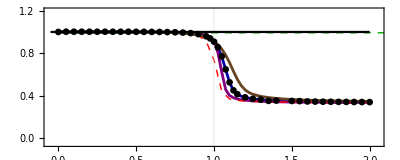

```mathematica
fig2a=Show[ListPlot[{DatCocR50,DatCocR100,DatCocR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,1.2}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],ListPlot[{DataCoCat},Joined->True,PlotStyle->{{Red,Dashed,Thick},{Darker[Yellow],Dashed,Thickness[0.004]}}],ListPlot[DataCoZq,Joined->True,PlotStyle->{Darker[Green],Dashed,Thick}],ListPlot[DataCoCl,Joined->False,PlotRange->All,PlotStyle->{Black,PointSize[0.012]}],Plot[1.0,{x,-0.05,2},PlotStyle->{Black}],AspectRatio->0.4]
```

#### (b) Momentum Kurtosis

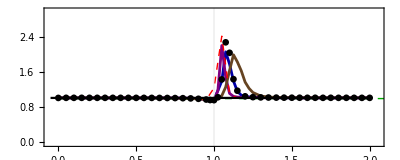

```mathematica
fig2b=Show[ListPlot[{DatCocPR50,DatCocPR100,DatCocPR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,3}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],ListPlot[{DataCoCat2},Joined->True,PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Darker[Yellow],Dashed,Thickness[0.004]}}],ListPlot[DataCoZq2,Joined->True,PlotStyle->{Darker[Green],Dashed,Thick}],ListPlot[DataCoCl2,Joined->False,PlotRange->All,PlotStyle->{Black,PointSize[0.012]}],Plot[1.0,{x,-0.05,2},PlotStyle->{Black}],AspectRatio->0.4]
```

#### (c) Impurity

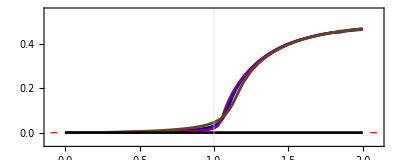

```mathematica
fig2c=Show[ListPlot[{DatImpR50,DatImpR100,DatImpR25},Joined->True,Frame->True,PlotRange->{{-0.1,2.1},{-0.05,0.55}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[0.0,{x,0,2},PlotStyle->{Black}],Plot[0.0,{x,-0.1,2.1},PlotStyle->{Red,Thickness[0.002],Dashed}],ListPlot[{DataImpCat},Joined->True,PlotRange->All,PlotStyle->{{Darker[Green]},{Darker[Yellow],Dashed,Thickness[0.004]}}],ListPlot[DataImpCl,Joined->True,PlotRange->All,PlotStyle->{Black}],AspectRatio->0.4]
```

#### (a) Wigner negativity

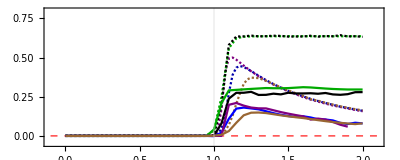

```mathematica
fig2d=Show[ListPlot[{DatNegR50,DatNegR100,DatNegR25},Frame->True,Joined->True,PlotRange->{{-0.1,2.1},{-0.05,0.8}},PlotStyle->{{Darker[Blue],Dashing[0.004,0.06]},{Purple,Dashing[0.004,0.06]},{Brown,Dashing[0.004,0.06]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[0.0,{x,-0.1,2.1},PlotStyle->{Red,Thickness[0.002],Dashed}],ListPlot[{DataNegCat},Joined->{True},PlotRange->All,PlotStyle->{{Darker[Green],Dashing[0.004,0.06]}}],ListPlot[{DataNegCl},Joined->True,PlotRange->All,PlotStyle->{{Black,Dashing[0.004,0.06]}}],
ListPlot[{DataWminCl,DatDeepestNegCat},Joined->True,PlotRange->All,PlotStyle->{Black,Darker[Green]}],
ListPlot[{WminR50,WminR100,DatDeepestR25},Joined->True,PlotStyle->{Blue,Purple,Brown}],AspectRatio->0.4]
```

#### (b) Squeezing destillation

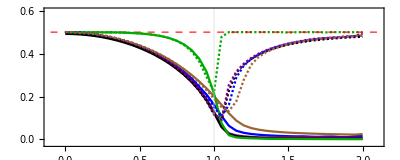

```mathematica
fig2e=Show[ListPlot[{DestSqueezingR50,DestSqueezingR100,DestSqueezingR25},Joined->True,Frame->True,PlotRange->{{-0.1,2.1},{-0.02,0.6}},PlotStyle->{{Blue},{Purple},{Brown}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],
ListPlot[{DataSqCl,VarpCat},Joined->True,PlotRange->All,PlotStyle->{{Black,Dashing[0.004,0.06]},{Darker[Green],Dashing[0.004,0.06]}}],Plot[0.5,{x,-0.1,2.1},PlotStyle->{{Red,Thickness[0.002],Dashed}}],
ListPlot[{DestSqueezingCl,SqDestCat},Joined->True,PlotRange->All,PlotStyle->{Black,Darker[Green]}],ListPlot[{SqueezingR50,SqueezingR100,SqueezingR25},Joined->True,PlotStyle->{{Blue,Dashing[0.004,0.06]},{Purple,Dashing[0.004,0.06]},{Brown,Dashing[0.004,0.06]}}],AspectRatio->0.4]
```

#### (c) Displacement sensitivity

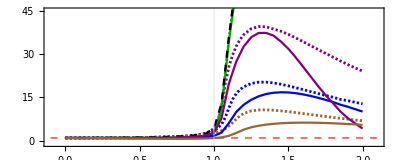

```mathematica
fig2e=Show[ListPlot[{DatQFIdisR50,DatQFIdisR100,DatQFIdisR25},Joined->True,Frame->True,PlotRange->{{-0.1,2.1},{-1.0,45}},PlotStyle->{{Blue,Thickness[0.005],Dashing[0.004,0.06]},{Purple,Thickness[0.005],Dashing[0.004,0.06]},{Brown,Thickness[0.005],Dashing[0.004,0.06]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[{1.0},{x,-0.1,2.1},PlotStyle->{{Red,Thickness[0.002],Dashed},{Darker[Green]}}],Plot[{FitCFICat[x]},{x,0.05,1.3},PlotStyle->{{Darker[Green]}}],ListPlot[{DataQFIdisCat},Joined->True,PlotRange->All,PlotStyle->{{Darker[Green],Dashing[0.004,0.06]},{Darker[Yellow],Dashed,Thickness[0.004]}}],ListPlot[DataQFICl1,Joined->True,PlotRange->All,PlotStyle->{Black,Dashed}],ListPlot[{DatCFIdispR50,DataCFIdisppcR100,DataCFIdispR25},Joined->True,PlotStyle->{Blue,Purple,Brown}],AspectRatio->0.4]
```

#### (f) Phase sensitivity

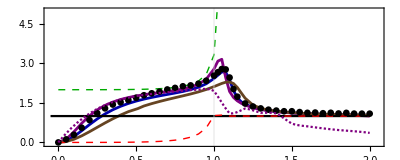

```mathematica
fig2f=Show[ListPlot[{QFIPR50,QFIPR100,QFIR25},Joined->True,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,5}},PlotStyle->{{Darker[Blue],Thickness[0.005]},{Purple,Thickness[0.005]},{Darker[Brown],Thickness[0.005]}},LabelStyle->{Black,12},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[1.0,{x,-0.05,2},PlotStyle->{Black}],ListPlot[{DataQFICat},Joined->True,PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Darker[Yellow],Dashed,Thickness[0.005]}}],ListPlot[DataQFIzq,Joined->True,PlotRange->All,PlotStyle->{Darker[Green],Dashed,Thick}],ListPlot[DataQFICl2,Joined->False,PlotRange->All,PlotStyle->{Black,PointSize[0.012]}],Plot[SPLCFIrotR100[x],{x,0.0,2},PlotRange->All,PlotStyle->{Purple,Dashing[0.004,0.06]}],AspectRatio->0.4]
```